```mathematica
Ber[m_,r_]:=r^m(r^-1 m)!/(m^m(m(r^-1-1))!)
legplaced=Placed[LineLegend[{1,0.8,0.6,0.4,.2},LegendFunction-> (Labeled[Panel[#],"Load Factor",Top]&)],Right]
```

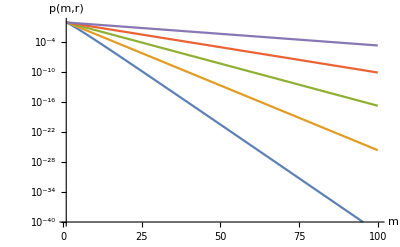

```mathematica
logplotber=LogPlot[
	{Ber[m,1],Ber[m,.8],Ber[m,.6],Ber[m,.4],Ber[m,.2]},{m,1.,100.},
	PlotRange->{10^-40,1},
	PlotLegends-> legplaced,
	AxesLabel->{m,p[m,r]}]
```

```mathematica
qBer[m_,r_]:=1-Ber[m,r]
```

```mathematica
fN[n_,m_,r_]:=qBer[m,r]^(2^n-1)(1-qBer[m,r]^(2^n))
```

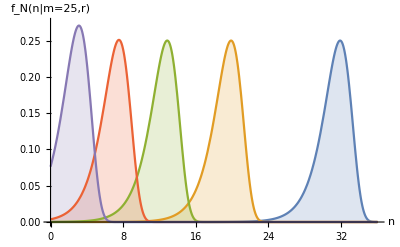

```mathematica
plotfn=Plot[
	{fN[n,25,1],fN[n,25,.8],fN[n,25,.6],fN[n,25,.4], fN[n,25,.2]},{n,0,36},
	Filling->Automatic,
	PlotRange->{0,.275},
	PlotLegends-> legplaced,
	AxesLabel->{n,"f_N(n|m=25,r)"}]
```

```mathematica
ExpN[m_,r_,nn_]:=Sum[n*N[fN[n,m,r],1000],{n,0,nn}]//N
```

```mathematica
data10=Table[{rr,ExpN[10,rr,30]},{rr,0.05,1,.05}]
```

```mathematica
data20=Table[{rr,ExpN[20,rr,33]},{rr,0.05,1,.05}]
```

{{0.05,0.440415},{0.1,0.908871},{0.15,1.43961},{0.2,2.03951},{0.25,2.70961},{0.3,3.44838},{0.35,4.25335},{0.4,5.12227},{0.45,6.05408},{0.5,7.04956},{0.55,8.11184},{0.6,9.2468},{0.65,10.4636},{0.7,11.7757},{0.75,13.2019},{0.8,14.77},{0.85,16.5217},{0.9,18.5265},{0.95,20.9164},{1.,24.0284}}

```mathematica
legListPlot=PointLegend[{10,20},
LegendMarkers->{Automatic},LegendFunction-> (Labeled[Panel[#],"Members",Top]&)]
```

PointLegend[{10,20},LegendMarkers→{Automatic},LegendFunction→(#1Members&)]

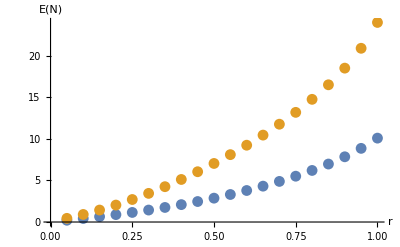

```mathematica
ListPlot[{data10,data20},
AxesLabel->{r,"E"[N]},
PlotLegends->legListPlot]
```

```mathematica
datamrhalf=Table[{mm,ExpN[mm,.5,1.25*mm]},{mm,5,35,5}]
datamrthreeq=Table[{mm,ExpN[mm,.75,1.25*mm]},{mm,5,35,5}]
```

{{5,1.12201},{10,2.87212},{15,4.89902},{20,7.04956},{25,9.24396},{30,11.4519},{35,13.6638}}

{{5,2.03507},{10,5.516},{15,9.33225},{20,13.2019},{25,17.0788},{30,20.9571},{35,24.836}}

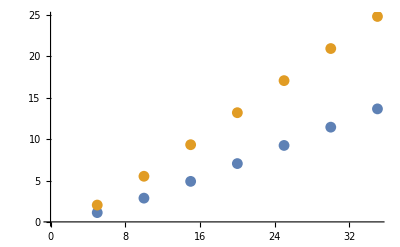

```mathematica
ListPlot[{datamrhalf,datamrthreeq}]
```

```mathematica
BerP[m_]:=Exp[-m]*(2*π*m)^(.5)//N
```

```mathematica
qBerP[m_]:=1-BerP[m]//N
```

```mathematica
fNP[n_,m_]:=qBerP[m]^(2^n-1)(1-qBerP[m]^(2^n))//N
```

```mathematica
ExpNP[m_,nn_]:=Sum[n*fNP[n,m],{n,0,nn}]//N
```

```mathematica
eval[m_,nx_]:=Sum[N[qBer[m,1],1000]^(2^n-1),{n,1,nx}]
evalr[m_,nx_,r_]:=Sum[N[qBer[m,r],1000]^(2^n-1),{n,1,nx}]
```

```mathematica
results=Table[{m,r/100,evalr[m,1.5*m,r/100]},{m,100,2000,100},{r,10,100,10}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

$Aborted

```mathematica
rs=N[results[[1]],5]
```

{{100.,0.1,6.102},{100.,0.2,14.005},{100.,0.3,22.613},{100.,0.4,32.024},{100.,0.5,42.437},{100.,0.6,54.148},{100.,0.7,67.629},{100.,0.8,83.731},{100.,0.9,104.38},{100.,1.,138.29}}

```mathematica
ListPointPlot3D[rs]
```

-Graphics3D-

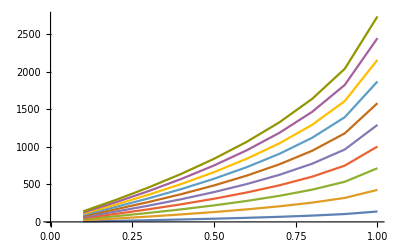

```mathematica
ListLinePlot[{results[[1,All,{2,3}]],results[[3,All,{2,3}]],results[[5,All,{2,3}]],results[[7,All,{2,3}]],results[[9,All,{2,3}]],results[[11,All,{2,3}]],results[[13,All,{2,3}]],results[[15,All,{2,3}]],results[[17,All,{2,3}]],results[[19,All,{2,3}]]}]
```

```mathematica
ListPointPlot3D[datat,AxesLabel->{m,r,"E[N]"},PlotTheme->"Monochrome"]
```

-Graphics3D-

```mathematica
fitted=FindFit[datat,a*m*b^r,{a,b},{m,r}]
```

{a→0.1167,b→12.23}

```mathematica
fitted=FindFit[datat,a*m*Exp[b*r],{a,b},{m,r}]
```

{a→0.1167,b→2.504}

```mathematica
fittedf[m_,r_]:=0.1171*m*12.19^r
fitted2=FindFit[datat,a*m*r,a,{m,r}]
```

```mathematica
fittedf[1000,1]
```

1427.45

```mathematica
Plot3D[fittedf[m,r],{m,1,10000},{r,0.1,1}]
```

```mathematica
datat=Flatten[N[results,4],1]
```

```mathematica
fitted=FindFit[datat,a*m*b^r,{a,b},{m,r}]
```

{a→0.1167,b→12.23}

```mathematica
ExpectedSize[m_,r_]:=0.1170*m*12.20^r
```

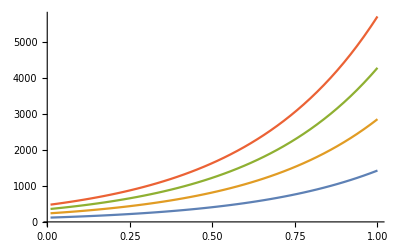

```mathematica
Plot[{ExpectedSize[1000,r],ExpectedSize[2000,r],ExpectedSize[3000,r],ExpectedSize[4000,r]},{r,0.01,1}]
```

```mathematica
Plot3D[ExpectedSize[m,r],{m,r}]
```

```mathematica
Plot3D[ExpectedSize[m,r],{m,100,1000},{r,0.01,1}]
```

```mathematica
ExpectedSize[m,1]
```

1.4274 m

```mathematica
m
```

m

```mathematica
r
```

r

```mathematica
fitted3=FindFit[datat2,1/Log[2]*m*b^(r-1),{b},{m,r}]
```

{b→12.58}

```mathematica
fff[m_,r_]:=1/Log[2]*m*12.54^(r-1)
```

```mathematica
nlm=NonlinearModelFit[datat[[20;;]],1/Log[2]*m*b^(r-1),{b},{m,r}]
```

FittedModel[((«44»)^(-1+r) m)/Log[2]]

```mathematica
FittedModel[((1.`4.)^(-1+r) m)/Log[2]]
```

FittedModel[(1.^(-1+r) m)/Log[2]]

```mathematica
nlm["BestFitParameters"]
```

{b→12.59}

```mathematica
N[nlm[{"BestFit","ParameterTable"}],4]
```

{1.443 12.6^(-1.+r) m, | Estimate | Standard Error | t-Statistic | P-Value
b | 12.6 | 0.2 | 70. | 0.}

```mathematica
1.443*12.54^-1
```

0.115072

```mathematica
nlm2=NonlinearModelFit[datat,a*m*b^r,{a,b},{m,r}]
```

FittedModel[0.1171 («44»)^r m]

```mathematica
N[nlm2[{"BestFit","ParameterTable"}],4]
```

{0.1171 12.19^r m, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.1171 | 0.002 | 60. | 0.
b | 12.19 | 0.24 | 52. | 0.}

```mathematica
evalTwo[m_,nx_]:=Sum[N[(1-BerTwo[m])^(2^n-1),1000],{n,1,nx}]
```

```mathematica
evalslope[m_,∞]:=Sum[N[qBer[m,1],2000]^(2^n-1),{n,1,nx}]-Sum[N[qBer[m-1,1],2000]^(2^n-1),{n,1,nx}]
```

```mathematica
evalslope[1750,2500]
```

0.000013067769400661389995716089505802435541606521558443818293838498160934504551104710384893000274734472055375094826119405590687304088488970907061573296792157855032527165765039162822932587572961577658150338647652450899658815667110947642299049820634985151945088182515401590857348176494949420567043833141321784255204233192346923038473148351293103668684953791311179831944407566194354185109923860202846061953479855281141722165385598553358204792563507019846645384217923568176372250884682223998074828102392451343698054776480936923158823210891447064032969638819608473161962872404320655701064859489476173351900440331437677342052799999644603254207326244496641680200454155385999666025570711177843950062537085085209716275223668388878068906493336801637155333590425217064865263422529212091421492674784975611738381352748576470939847035076925740282342920073591660621563896517477872786418688346220655121450081152237743027110803266906360252638271401643265790533845299764739138701040755636761427191983185889135136454529239620436890773082428785172044674177792275407663484559712549763042121744494568712563148275592476426068955405577636270692260963155525661468492499398930877726866886450916554404221665128861192905468454370543762269715485999348361793834838656229941275

```mathematica
1/Log[2]//N
```

1.4427

```mathematica
D[Sum[qBer[m,1]^(2^n-1),{n,1,∞}],m]
```

```mathematica
qmr[mm_,nn_]:=(1-Exp[-mm]*Sqrt[2*π*mm])^(2^nn-1)
```

```mathematica
dqmr[mm_,nn_]:=D[qmr[mm,nn],mm]
```

((-1+2^n) ⅇ^m (-1+2 m) √(π/2) (1-ⅇ^-m √m √(2 π))^(2^n))/(√m (ⅇ^m-√m √(2 π))^2)

```mathematica
innerpart[mm_,nn_]:=(1-Exp[-mm]*Sqrt[2*π*mm])^(2^nn-1)(2^nn-1)
```

```mathematica
innerpart[m,n]
```

(-1+2^n) (1-ⅇ^-m √m √(2 π))^(-1+2^n)

```mathematica
Limit[innerpart[m,n],m->∞]
```

-1+2^n

```mathematica
Simplify[Limit[(-1+2^n) (1-ⅇ^-m √m √(2 π))^(-1+2^n),n->∞]]
```

Limit[(-1+2^n) (1-ⅇ^-m √m √(2 π))^(-1+2^n),n→∞]

```mathematica
Ber[m,1]
```

m^-m m!

```mathematica
compute[mm_,nn_]:=N[Ber[mm,1],2000]*Sum[(1-N[Ber[mm,1],2000])^(2^n-1)*(2^n-1),{n,1,nn}]
```

```mathematica
resultstwo=Table[N[compute[mm,1.5*mm]-1/Log[2],10],{mm,10,1000,10}]
```

$Aborted

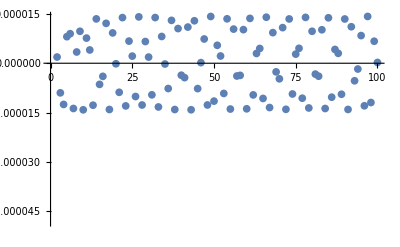

```mathematica
ListPlot[resultstwo]
```

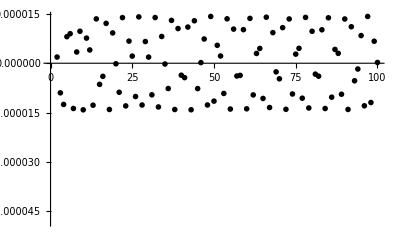

```mathematica
ListPlot[resultstwo,PlotTheme->"Monochrome"]
```

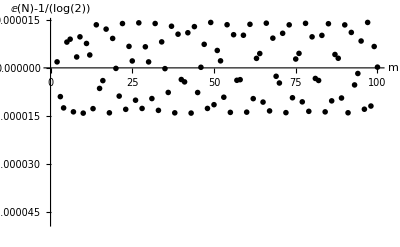

```mathematica
Show[%581,AxesLabel->{HoldForm[m],HoldForm[ⅇ[N]-1/Log[2]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%582,Background->None]
```

-Graphics-

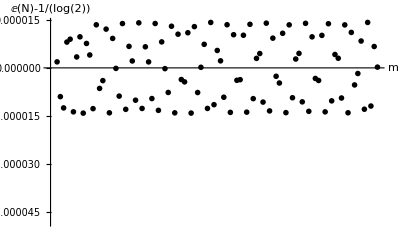

```mathematica
Show[%583,Ticks->{None,Automatic},AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.265]]]
```

```mathematica
Show[%583,Axes->False,]
```

```mathematica
ListPlot[{{Range[10,1000,10],resultstwo}}]
```

ListPlot[{{{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,970,980,990,1000},{-0.004132417035,1.88383638×10^-6,-9.003596465×10^-6,-0.00001253122581,8.072777323×10^-6,8.978271527×10^-6,-0.00001375834094,3.415342641×10^-6,9.719472869×10^-6,-0.00001416636661,7.643829463×10^-6,4.037514426×10^-6,-0.00001276231417,0.00001348153549,-6.426154409×10^-6,-3.99166504×10^-6,0.00001213021688,-0.00001406844686,9.217104064×10^-6,-1.643880009×10^-7,-8.837633128×10^-6,0.00001387583393,-0.00001297636907,6.729661231×10^-6,2.165022353×10^-6,-0.00001012017974,0.00001409620757,-0.00001270174022,6.597305424×10^-6,1.870994448×10^-6,-9.606031376×10^-6,0.00001388832323,-0.00001329783061,8.135100228×10^-6,-2.393123717×10^-7,-7.693147932×10^-6,0.00001303326578,-0.00001407366078,0.00001054417965,-3.645523198×10^-6,-4.38201011×10^-6,0.00001099548335,-0.00001414948591,0.00001291144695,-7.713989199×10^-6,1.852854607×10^-7,7.373598991×10^-6,-0.00001269455896,0.00001421530296,-0.00001152325529,5.450027965×10^-6,2.198760332×10^-6,-9.187737413×10^-6,0.00001350449601,-0.0000139316013,0.00001037821056,-3.884526712×10^-6,-3.692189612×10^-6,0.0000102131562,-0.00001386053293,0.00001363773582,-9.632059774×10^-6,2.973905521×10^-6,4.489233714×10^-6,-0.00001070863135,0.00001399509389,-0.00001347227255,9.302845034×10^-6,-2.631032442×10^-6,-4.737046133×10^-6,0.00001082448253,-0.00001401278626,0.00001346785006,-9.351767763×10^-6,2.769070624×10^-6,4.534213301×10^-6,-0.00001063587124,0.00001394235627,-0.00001360136882,9.716633302×10^-6,-3.31168512×10^-6,-3.943834563×10^-6,0.00001017113555,-0.00001376832739,0.00001381975967,-0.00001032475097,4.19026664×10^-6,3.007925829×10^-6,-9.432053128×10^-6,0.00001345120247,-0.00001405323264,0.00001109641108,-5.338655832×10^-6,-1.759929828×10^-6,8.409040942×10^-6,-0.00001294000948,0.0000142230382,-0.00001194599823,6.687210946×10^-6,2.343562542×10^-7}}}]

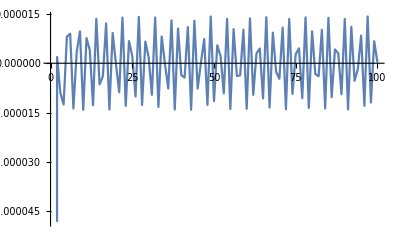

```mathematica
ListLinePlot[resultstwo]
```

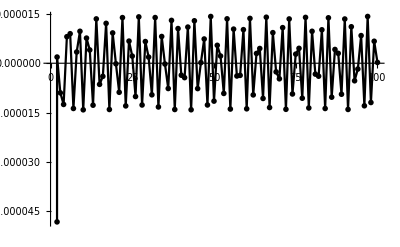

```mathematica
ListLinePlot[resultstwo,PlotTheme->"Monochrome"]
```

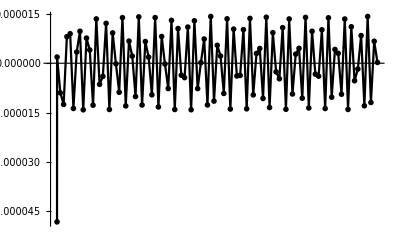

```mathematica
Show[%587,Ticks->{None,Automatic}]
```

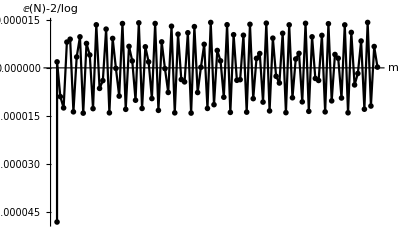

```mathematica
Show[%588,AxesLabel->{HoldForm[m],HoldForm[ⅇ[N]-2/log]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
resultsthree=Table[N[compute[mm,1.5*mm]-1/Log[2],10],{mm,1010,2000,10}]
```

{-7.091943934×10^-6,0.00001218207924,-0.00001424675974,0.00001278228797,-8.159155603×10^-6,1.525751151×10^-6,5.47871064×10^-6,-0.00001113019024,0.00001404350898,-0.00001351007618,9.66804874×10^-6,-3.46410742×10^-6,-3.581780878×10^-6,9.749540137×10^-6,-0.00001353885542,0.00001403292984,-0.00001111815815,5.508131162×10^-6,1.432924499×10^-6,-8.023200264×10^-6,0.0000126708023,-0.00001425747538,0.00001240623534,-7.568811688×10^-6,9.13674948×10^-7,5.957347072×10^-6,-0.00001139525238,0.00001409908941,-0.00001342588412,9.542063781×10^-6,-3.380544538×10^-6,-3.584772479×10^-6,9.692072015×10^-6,-0.00001348812931,0.00001407328183,-0.00001131308784,5.867775029×10^-6,9.670425297×10^-7,-7.569658089×10^-6,0.00001237705771,-0.00001425442733,0.00001276207484,-8.256826943×10^-6,1.805447761×10^-6,5.068830119×10^-6,-0.00001074656782,0.00001389329231,-0.00001377225649,0.0000104159381,-4.616053632×10^-6,-2.26429918×10^-6,8.611432893×10^-6,-0.00001293973493,0.00001423886049,-0.00001220844921,7.326580608×10^-6,-7.36090778×10^-7,-6.023857063×10^-6,0.00001137731223,-0.00001407875013,0.00001350222801,-9.785212203×10^-6,3.794882819×10^-6,3.074963072×10^-6,-9.228862124×10^-6,0.00001324004622,-0.00001418071997,0.00001183600022,-6.751843944×10^-6,1.070557656×10^-7,6.560483786×10^-6,-0.00001171012603,0.00001415412363,-0.00001333082289,9.433067388×10^-6,-3.362049242×10^-6,-3.481835114×10^-6,9.522187656×10^-6,-0.0000133698072,0.00001414178653,-0.00001166321203,6.506123067×10^-6,1.432734894×10^-7,-6.758109729×10^-6,0.00001182142535,-0.00001417387259,0.00001327874177,-9.343471138×10^-6,3.270926052×10^-6,3.54826177×10^-6,-9.554660532×10^-6,0.00001337647521,-0.00001414243862,0.00001167999821,-6.553295199×10^-6,-6.671613819×10^-8,6.670001144×10^-6,-0.00001175220978,0.0000141571404,-0.00001333918112}

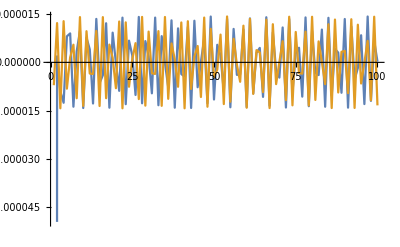

```mathematica
ListLinePlot[{resultstwo,resultsthree}]
```

```mathematica
resultsfour=Table[{mm,N[compute[mm,1.5*mm]-1/Log[2],10]},{mm,2010,3000,10}]
```

{{2010,9.486652618×10^-6},{2020,-3.477694698×10^-6},{2030,-3.320499869×10^-6},{2040,9.362843052×10^-6},{2050,-0.00001327763965},{2060,0.00001417769649},{2070,-0.00001186067374},{2080,6.854120804×10^-6},{2090,-2.947706465×10^-7},{2100,-6.33009998×10^-6},{2110,0.00001151983772},{2120,-0.00001410025466},{2130,0.0000134890035},{2140,-9.826249038×10^-6},{2150,3.942071965×10^-6},{2160,2.83205479×10^-6},{2170,-8.96500873×10^-6},{2180,0.00001307193701},{2190,-0.00001422669022},{2200,0.00001217039693},{2210,-7.368769228×10^-6},{2220,9.061546112×10^-7},{2230,5.759565322×10^-6},{2240,-0.00001112619156},{2250,0.00001398554792},{2260,-0.00001369504327},{2270,0.00001032180482},{2280,-4.626534847×10^-6},{2290,-2.10851468×10^-6},{2300,8.368301266×10^-6},{2310,-0.00001274599336},{2320,0.00001425893551},{2330,-0.00001256867807},{2340,8.056402483×10^-6},{2350,-1.736441041×10^-6},{2360,-4.972205382×10^-6},{2370,0.00001056442143},{2380,-0.00001378669364},{2390,0.00001391789314},{2400,-0.00001093005291},{2410,5.494007899×10^-6},{2420,1.171595376×10^-6},{2430,-7.573923101×10^-6},{2440,0.00001228016403},{2450,-0.00001423806464},{2460,0.00001301102103},{2470,-8.87482307×10^-6},{2480,2.755335809×10^-6},{2490,3.97897605×10^-6},{2500,-9.823434503×10^-6},{2510,0.00001347318142},{2520,-0.00001411423995},{2530,0.00001160488541},{2540,-6.506399563×10^-6},{2550,-4.283621082×10^-8},{2560,6.581607834×10^-6},{2570,-0.00001165215621},{2580,0.00001412500193},{2590,-0.00001345015344},{2600,9.779269036×10^-6},{2610,-3.931082491×10^-6},{2620,-2.791585416×10^-6},{2630,8.892041891×10^-6},{2640,-0.00001301309627},{2650,0.00001423884618},{2660,-0.00001229776461},{2670,7.622671605×10^-6},{2680,-1.25383794×10^-6},{2690,-5.392876388×10^-6},{2700,0.00001084068582},{2710,-0.00001388002894},{2720,0.00001383699766},{2730,-0.00001072224513},{2740,5.228173621×10^-6},{2750,1.425250996×10^-6},{2760,-7.761764412×10^-6},{2770,0.00001237621585},{2780,-0.00001424607084},{2790,0.00001295789895},{2800,-8.79826451×10^-6},{2810,2.689740011×10^-6},{2820,4.013858565×10^-6},{2830,-9.827842248×10^-6},{2840,0.00001346531645},{2850,-0.00001412181141},{2860,0.00001165311829},{2870,-6.606480869×10^-6},{2880,9.900921838×10^-8},{2890,6.429638015×10^-6},{2900,-0.00001153601277},{2910,0.00001409187033},{2920,-0.00001353313334},{2930,9.984305738×10^-6},{2940,-4.23031422×10^-6},{2950,-2.457411393×10^-6},{2960,8.601828899×10^-6},{2970,-0.00001284667479},{2980,0.00001425571486},{2990,-0.00001251884189},{3000,8.020234993×10^-6}}

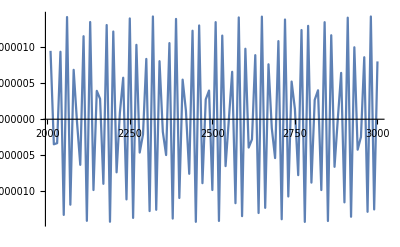

```mathematica
ListLinePlot[resultsfour]
```

```mathematica
Range[10,1000,10]
```

{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,970,980,990,1000}

```mathematica
resultsB=MapThread[List,{Range[1010,2000,10],resultsthree}]
```

{{1010,-7.091943934×10^-6},{1020,0.00001218207924},{1030,-0.00001424675974},{1040,0.00001278228797},{1050,-8.159155603×10^-6},{1060,1.525751151×10^-6},{1070,5.47871064×10^-6},{1080,-0.00001113019024},{1090,0.00001404350898},{1100,-0.00001351007618},{1110,9.66804874×10^-6},{1120,-3.46410742×10^-6},{1130,-3.581780878×10^-6},{1140,9.749540137×10^-6},{1150,-0.00001353885542},{1160,0.00001403292984},{1170,-0.00001111815815},{1180,5.508131162×10^-6},{1190,1.432924499×10^-6},{1200,-8.023200264×10^-6},{1210,0.0000126708023},{1220,-0.00001425747538},{1230,0.00001240623534},{1240,-7.568811688×10^-6},{1250,9.13674948×10^-7},{1260,5.957347072×10^-6},{1270,-0.00001139525238},{1280,0.00001409908941},{1290,-0.00001342588412},{1300,9.542063781×10^-6},{1310,-3.380544538×10^-6},{1320,-3.584772479×10^-6},{1330,9.692072015×10^-6},{1340,-0.00001348812931},{1350,0.00001407328183},{1360,-0.00001131308784},{1370,5.867775029×10^-6},{1380,9.670425297×10^-7},{1390,-7.569658089×10^-6},{1400,0.00001237705771},{1410,-0.00001425442733},{1420,0.00001276207484},{1430,-8.256826943×10^-6},{1440,1.805447761×10^-6},{1450,5.068830119×10^-6},{1460,-0.00001074656782},{1470,0.00001389329231},{1480,-0.00001377225649},{1490,0.0000104159381},{1500,-4.616053632×10^-6},{1510,-2.26429918×10^-6},{1520,8.611432893×10^-6},{1530,-0.00001293973493},{1540,0.00001423886049},{1550,-0.00001220844921},{1560,7.326580608×10^-6},{1570,-7.36090778×10^-7},{1580,-6.023857063×10^-6},{1590,0.00001137731223},{1600,-0.00001407875013},{1610,0.00001350222801},{1620,-9.785212203×10^-6},{1630,3.794882819×10^-6},{1640,3.074963072×10^-6},{1650,-9.228862124×10^-6},{1660,0.00001324004622},{1670,-0.00001418071997},{1680,0.00001183600022},{1690,-6.751843944×10^-6},{1700,1.070557656×10^-7},{1710,6.560483786×10^-6},{1720,-0.00001171012603},{1730,0.00001415412363},{1740,-0.00001333082289},{1750,9.433067388×10^-6},{1760,-3.362049242×10^-6},{1770,-3.481835114×10^-6},{1780,9.522187656×10^-6},{1790,-0.0000133698072},{1800,0.00001414178653},{1810,-0.00001166321203},{1820,6.506123067×10^-6},{1830,1.432734894×10^-7},{1840,-6.758109729×10^-6},{1850,0.00001182142535},{1860,-0.00001417387259},{1870,0.00001327874177},{1880,-9.343471138×10^-6},{1890,3.270926052×10^-6},{1900,3.54826177×10^-6},{1910,-9.554660532×10^-6},{1920,0.00001337647521},{1930,-0.00001414243862},{1940,0.00001167999821},{1950,-6.553295199×10^-6},{1960,-6.671613819×10^-8},{1970,6.670001144×10^-6},{1980,-0.00001175220978},{1990,0.0000141571404},{2000,-0.00001333918112}}

```mathematica
allresultsA=Join[resultsA,resultsB,resultsfour]
```

{{10,-0.004132417035},{20,1.88383638×10^-6},{30,-9.003596465×10^-6},{40,-0.00001253122581},{50,8.072777323×10^-6},{60,8.978271527×10^-6},{70,-0.00001375834094},{80,3.415342641×10^-6},{90,9.719472869×10^-6},{100,-0.00001416636661},{110,7.643829463×10^-6},{120,4.037514426×10^-6},{130,-0.00001276231417},{140,0.00001348153549},{150,-6.426154409×10^-6},{160,-3.99166504×10^-6},{170,0.00001213021688},{180,-0.00001406844686},{190,9.217104064×10^-6},{200,-1.643880009×10^-7},{210,-8.837633128×10^-6},{220,0.00001387583393},{230,-0.00001297636907},{240,6.729661231×10^-6},{250,2.165022353×10^-6},{260,-0.00001012017974},{270,0.00001409620757},{280,-0.00001270174022},{290,6.597305424×10^-6},{300,1.870994448×10^-6},{310,-9.606031376×10^-6},{320,0.00001388832323},{330,-0.00001329783061},{340,8.135100228×10^-6},{350,-2.393123717×10^-7},{360,-7.693147932×10^-6},{370,0.00001303326578},{380,-0.00001407366078},{390,0.00001054417965},{400,-3.645523198×10^-6},{410,-4.38201011×10^-6},{420,0.00001099548335},{430,-0.00001414948591},{440,0.00001291144695},{450,-7.713989199×10^-6},{460,1.852854607×10^-7},{470,7.373598991×10^-6},{480,-0.00001269455896},{490,0.00001421530296},{500,-0.00001152325529},{510,5.450027965×10^-6},{520,2.198760332×10^-6},{530,-9.187737413×10^-6},{540,0.00001350449601},{550,-0.0000139316013},{560,0.00001037821056},{570,-3.884526712×10^-6},{580,-3.692189612×10^-6},{590,0.0000102131562},{600,-0.00001386053293},{610,0.00001363773582},{620,-9.632059774×10^-6},{630,2.973905521×10^-6},{640,4.489233714×10^-6},{650,-0.00001070863135},{660,0.00001399509389},{670,-0.00001347227255},{680,9.302845034×10^-6},{690,-2.631032442×10^-6},{700,-4.737046133×10^-6},{710,0.00001082448253},{720,-0.00001401278626},{730,0.00001346785006},{740,-9.351767763×10^-6},{750,2.769070624×10^-6},{760,4.534213301×10^-6},{770,-0.00001063587124},{780,0.00001394235627},{790,-0.00001360136882},{800,9.716633302×10^-6},{810,-3.31168512×10^-6},{820,-3.943834563×10^-6},{830,0.00001017113555},{840,-0.00001376832739},{850,0.00001381975967},{860,-0.00001032475097},{870,4.19026664×10^-6},{880,3.007925829×10^-6},{890,-9.432053128×10^-6},{900,0.00001345120247},{910,-0.00001405323264},{920,0.00001109641108},{930,-5.338655832×10^-6},{940,-1.759929828×10^-6},{950,8.409040942×10^-6},{960,-0.00001294000948},{970,0.0000142230382},{980,-0.00001194599823},{990,6.687210946×10^-6},{1000,2.343562542×10^-7},{1010,-7.091943934×10^-6},{1020,0.00001218207924},{1030,-0.00001424675974},{1040,0.00001278228797},{1050,-8.159155603×10^-6},{1060,1.525751151×10^-6},{1070,5.47871064×10^-6},{1080,-0.00001113019024},{1090,0.00001404350898},{1100,-0.00001351007618},{1110,9.66804874×10^-6},{1120,-3.46410742×10^-6},{1130,-3.581780878×10^-6},{1140,9.749540137×10^-6},{1150,-0.00001353885542},{1160,0.00001403292984},{1170,-0.00001111815815},{1180,5.508131162×10^-6},{1190,1.432924499×10^-6},{1200,-8.023200264×10^-6},{1210,0.0000126708023},{1220,-0.00001425747538},{1230,0.00001240623534},{1240,-7.568811688×10^-6},{1250,9.13674948×10^-7},{1260,5.957347072×10^-6},{1270,-0.00001139525238},{1280,0.00001409908941},{1290,-0.00001342588412},{1300,9.542063781×10^-6},{1310,-3.380544538×10^-6},{1320,-3.584772479×10^-6},{1330,9.692072015×10^-6},{1340,-0.00001348812931},{1350,0.00001407328183},{1360,-0.00001131308784},{1370,5.867775029×10^-6},{1380,9.670425297×10^-7},{1390,-7.569658089×10^-6},{1400,0.00001237705771},{1410,-0.00001425442733},{1420,0.00001276207484},{1430,-8.256826943×10^-6},{1440,1.805447761×10^-6},{1450,5.068830119×10^-6},{1460,-0.00001074656782},{1470,0.00001389329231},{1480,-0.00001377225649},{1490,0.0000104159381},{1500,-4.616053632×10^-6},{1510,-2.26429918×10^-6},{1520,8.611432893×10^-6},{1530,-0.00001293973493},{1540,0.00001423886049},{1550,-0.00001220844921},{1560,7.326580608×10^-6},{1570,-7.36090778×10^-7},{1580,-6.023857063×10^-6},{1590,0.00001137731223},{1600,-0.00001407875013},{1610,0.00001350222801},{1620,-9.785212203×10^-6},{1630,3.794882819×10^-6},{1640,3.074963072×10^-6},{1650,-9.228862124×10^-6},{1660,0.00001324004622},{1670,-0.00001418071997},{1680,0.00001183600022},{1690,-6.751843944×10^-6},{1700,1.070557656×10^-7},{1710,6.560483786×10^-6},{1720,-0.00001171012603},{1730,0.00001415412363},{1740,-0.00001333082289},{1750,9.433067388×10^-6},{1760,-3.362049242×10^-6},{1770,-3.481835114×10^-6},{1780,9.522187656×10^-6},{1790,-0.0000133698072},{1800,0.00001414178653},{1810,-0.00001166321203},{1820,6.506123067×10^-6},{1830,1.432734894×10^-7},{1840,-6.758109729×10^-6},{1850,0.00001182142535},{1860,-0.00001417387259},{1870,0.00001327874177},{1880,-9.343471138×10^-6},{1890,3.270926052×10^-6},{1900,3.54826177×10^-6},{1910,-9.554660532×10^-6},{1920,0.00001337647521},{1930,-0.00001414243862},{1940,0.00001167999821},{1950,-6.553295199×10^-6},{1960,-6.671613819×10^-8},{1970,6.670001144×10^-6},{1980,-0.00001175220978},{1990,0.0000141571404},{2000,-0.00001333918112},{2010,9.486652618×10^-6},{2020,-3.477694698×10^-6},{2030,-3.320499869×10^-6},{2040,9.362843052×10^-6},{2050,-0.00001327763965},{2060,0.00001417769649},{2070,-0.00001186067374},{2080,6.854120804×10^-6},{2090,-2.947706465×10^-7},{2100,-6.33009998×10^-6},{2110,0.00001151983772},{2120,-0.00001410025466},{2130,0.0000134890035},{2140,-9.826249038×10^-6},{2150,3.942071965×10^-6},{2160,2.83205479×10^-6},{2170,-8.96500873×10^-6},{2180,0.00001307193701},{2190,-0.00001422669022},{2200,0.00001217039693},{2210,-7.368769228×10^-6},{2220,9.061546112×10^-7},{2230,5.759565322×10^-6},{2240,-0.00001112619156},{2250,0.00001398554792},{2260,-0.00001369504327},{2270,0.00001032180482},{2280,-4.626534847×10^-6},{2290,-2.10851468×10^-6},{2300,8.368301266×10^-6},{2310,-0.00001274599336},{2320,0.00001425893551},{2330,-0.00001256867807},{2340,8.056402483×10^-6},{2350,-1.736441041×10^-6},{2360,-4.972205382×10^-6},{2370,0.00001056442143},{2380,-0.00001378669364},{2390,0.00001391789314},{2400,-0.00001093005291},{2410,5.494007899×10^-6},{2420,1.171595376×10^-6},{2430,-7.573923101×10^-6},{2440,0.00001228016403},{2450,-0.00001423806464},{2460,0.00001301102103},{2470,-8.87482307×10^-6},{2480,2.755335809×10^-6},{2490,3.97897605×10^-6},{2500,-9.823434503×10^-6},{2510,0.00001347318142},{2520,-0.00001411423995},{2530,0.00001160488541},{2540,-6.506399563×10^-6},{2550,-4.283621082×10^-8},{2560,6.581607834×10^-6},{2570,-0.00001165215621},{2580,0.00001412500193},{2590,-0.00001345015344},{2600,9.779269036×10^-6},{2610,-3.931082491×10^-6},{2620,-2.791585416×10^-6},{2630,8.892041891×10^-6},{2640,-0.00001301309627},{2650,0.00001423884618},{2660,-0.00001229776461},{2670,7.622671605×10^-6},{2680,-1.25383794×10^-6},{2690,-5.392876388×10^-6},{2700,0.00001084068582},{2710,-0.00001388002894},{2720,0.00001383699766},{2730,-0.00001072224513},{2740,5.228173621×10^-6},{2750,1.425250996×10^-6},{2760,-7.761764412×10^-6},{2770,0.00001237621585},{2780,-0.00001424607084},{2790,0.00001295789895},{2800,-8.79826451×10^-6},{2810,2.689740011×10^-6},{2820,4.013858565×10^-6},{2830,-9.827842248×10^-6},{2840,0.00001346531645},{2850,-0.00001412181141},{2860,0.00001165311829},{2870,-6.606480869×10^-6},{2880,9.900921838×10^-8},{2890,6.429638015×10^-6},{2900,-0.00001153601277},{2910,0.00001409187033},{2920,-0.00001353313334},{2930,9.984305738×10^-6},{2940,-4.23031422×10^-6},{2950,-2.457411393×10^-6},{2960,8.601828899×10^-6},{2970,-0.00001284667479},{2980,0.00001425571486},{2990,-0.00001251884189},{3000,8.020234993×10^-6}}

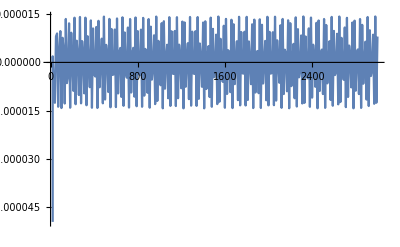

```mathematica
ListLinePlot[allresultsA]
```

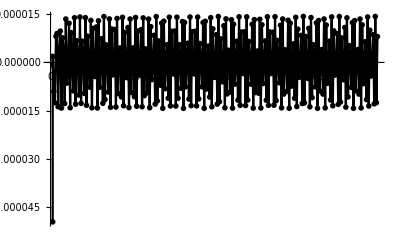

```mathematica
ListLinePlot[allresultsA,PlotTheme->"Monochrome"]
```

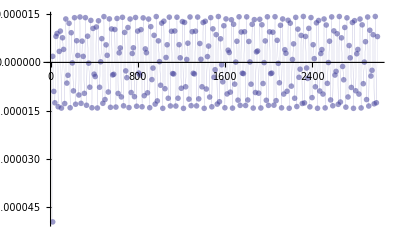

```mathematica
ListLinePlot[allresultsA,PlotStyle->Directive[Opacity[0.524],AbsoluteThickness[0.]],PlotTheme->"Monochrome"]
```

```mathematica
alldatahere={{10,-0.00413241703467860290654792603019455461`10.},{20,1.88383638018225150328827445629511`10.*^-6},{30,-9.0035964652615315653482267406647`10.*^-6},{40,-0.00001253122581487102144952600056115294`10.},{50,8.07277732325249006946704748526398`10.*^-6},{60,8.97827152710366213311716926889823`10.*^-6},{70,-0.00001375834093909501436875461213496045`10.},{80,3.41534264072492288290801023365842`10.*^-6},{90,9.71947286886245505320689320849236`10.*^-6},{100,-0.00001416636661394395882506172776331894`10.},{110,7.6438294629383223422560491362189`10.*^-6},{120,4.03751442592317922048003750362455`10.*^-6},{130,-0.00001276231417460457195650490597223525`10.},{140,0.00001348153549170579453160410488319818`10.},{150,-6.42615440912593486474339277749764`10.*^-6},{160,-3.9916650402314064893613485074247`10.*^-6},{170,0.00001213021688240675404932727237284447`10.},{180,-0.00001406844685676897249322185678552932`10.},{190,9.2171040640390444583754273010278`10.*^-6},{200,-1.6438800086841149292794659580958`10.*^-7},{210,-8.83763312764226645452620251155121`10.*^-6},{220,0.00001387583393440684690798706436136906`10.},{230,-0.00001297636906590369405987880983312887`10.},{240,6.7296612307245448944065108488683`10.*^-6},{250,2.16502235313637490838910804034231`10.*^-6},{260,-0.00001012017974140194265815511953548255`10.},{270,0.00001409620756881230694705169031880093`10.},{280,-0.00001270174022275263248830167821629781`10.},{290,6.59730542422204045828864359554921`10.*^-6},{300,1.87099444848264253519057096766082`10.*^-6},{310,-9.60603137640305190084030721240173`10.*^-6},{320,0.0000138883232338572048056125774593143`10.},{330,-0.00001329783061109027291832186772008092`10.},{340,8.13510022845851776067595819112282`10.*^-6},{350,-2.3931237172699915795608458801879`10.*^-7},{360,-7.69314793184643930726892203656859`10.*^-6},{370,0.00001303326577625995982544594773131475`10.},{380,-0.00001407366077986409694739409519665967`10.},{390,0.00001054417965384381575674210016330822`10.},{400,-3.64552319825946046650939973114029`10.*^-6},{410,-4.38201010978893603662119145220892`10.*^-6},{420,0.00001099548334532111002912118785672902`10.},{430,-0.0000141494859109052543875732844401506`10.},{440,0.00001291144694680323354472914973264888`10.},{450,-7.71398919925022857208697000973887`10.*^-6},{460,1.8528546070631429838191836547558`10.*^-7},{470,7.373598991209860498012533890619`10.*^-6},{480,-0.00001269455896368858894801260298710629`10.},{490,0.00001421530295777628741848397490494427`10.},{500,-0.00001152325529219453067574199749965102`10.},{510,5.45002796479189138773542588634463`10.*^-6},{520,2.19876033181115937843510935118537`10.*^-6},{530,-9.18773741346010690555510464425537`10.*^-6},{540,0.00001350449601329104530638725231161382`10.},{550,-0.00001393160130223396312619709243124773`10.},{560,0.00001037821055881133851747901074460869`10.},{570,-3.8845267120648239280087070402501`10.*^-6},{580,-3.6921896122294031179608070849836`10.*^-6},{590,0.00001021315619754135703699284560587065`10.},{600,-0.00001386053292878252931951981715060606`10.},{610,0.00001363773581618926476969204193551613`10.},{620,-9.6320597742982839987333773696999`10.*^-6},{630,2.97390552085642322690711634539845`10.*^-6},{640,4.48923371354838401449205636595067`10.*^-6},{650,-0.00001070863135408138308163020544544752`10.},{660,0.00001399509388632272230488118968107479`10.},{670,-0.0000134722725515643301320224068508285`10.},{680,9.30284503425049374747352365426961`10.*^-6},{690,-2.63103244202969944870038774289631`10.*^-6},{700,-4.73704613289113253216074092846168`10.*^-6},{710,0.00001082448252515541228912871114425771`10.},{720,-0.00001401278625604090751760683727797876`10.},{730,0.00001346785006282526659932642082493025`10.},{740,-9.35176776266702503213195587222487`10.*^-6},{750,2.76907062441287331303604472348921`10.*^-6},{760,4.53421330112441992194657446309634`10.*^-6},{770,-0.00001063587124455442653676303226440049`10.},{780,0.00001394235626579564558170177538590773`10.},{790,-0.0000136013688223896905118414379201615`10.},{800,9.71663330192433132946469847340528`10.*^-6},{810,-3.31168511972713454137414417989959`10.*^-6},{820,-3.94383456292516673164396723690335`10.*^-6},{830,0.00001017113554626539501809988788029578`10.},{840,-0.00001376832739171102873029506739433855`10.},{850,0.00001381975966720994447796145752525236`10.},{860,-0.00001032475096881998487631781558107012`10.},{870,4.19026664001048024611875897174465`10.*^-6},{880,3.00792582870228000808502193179698`10.*^-6},{890,-9.4320531277094042771686425721483`10.*^-6},{900,0.00001345120247075456411856853903062173`10.},{910,-0.00001405323264183941181250236075732697`10.},{920,0.00001109641107789859566196192957107584`10.},{930,-5.33865583154499602259649112865517`10.*^-6},{940,-1.75992982783698143657541746398499`10.*^-6},{950,8.40904094170523229807215482991425`10.*^-6},{960,-0.00001294000948181100629892873338164095`10.},{970,0.00001422303819519337817188931094864512`10.},{980,-0.00001194599822752045409858228869012519`10.},{990,6.6872109461678383976370614768792`10.*^-6},{1000,2.3435625417181161484000908779752`10.*^-7},{1010,-7.09194393363489908951741241641471`10.*^-6},{1020,0.0000121820792435521967008045158833394`10.},{1030,-0.00001424675973722235955415600048816793`10.},{1040,0.00001278228796701270520398768648711443`10.},{1050,-8.15915560307638145210103348814507`10.*^-6},{1060,1.52575115112930753253543878340094`10.*^-6},{1070,5.47871064004491198599052926446882`10.*^-6},{1080,-0.00001113019024487227503134735763686811`10.},{1090,0.00001404350898359996769083856116773954`10.},{1100,-0.00001351007618334441489700772185325619`10.},{1110,9.66804874025908726253223088984388`10.*^-6},{1120,-3.46410741984432886905567227058371`10.*^-6},{1130,-3.58178087760743917829863497609861`10.*^-6},{1140,9.74954013657790088942494748713582`10.*^-6},{1150,-0.00001353885541618405751260222019379306`10.},{1160,0.00001403292984252022102347946217308178`10.},{1170,-0.00001111815815155736241567461984967209`10.},{1180,5.50813116191213076213041205154779`10.*^-6},{1190,1.4329244992106409062217058201286`10.*^-6},{1200,-8.02320026379690226493205351213767`10.*^-6},{1210,0.00001267080230336212557632850548749329`10.},{1220,-0.00001425747537583779489381167307299558`10.},{1230,0.00001240623534283821084013258930137861`10.},{1240,-7.56881168754474413363656131790767`10.*^-6},{1250,9.1367494803279164811217766169087`10.*^-7},{1260,5.95734707208402560140769741212973`10.*^-6},{1270,-0.00001139525238224941955445189521864812`10.},{1280,0.00001409908940695492325934886059589288`10.},{1290,-0.00001342588412455162640965347820906174`10.},{1300,9.54206378133147996179621642432076`10.*^-6},{1310,-3.38054453773064014438514596151779`10.*^-6},{1320,-3.58477247907085187204232452034351`10.*^-6},{1330,9.69207201496715723750903634225569`10.*^-6},{1340,-0.00001348812930958951577435194266176267`10.},{1350,0.00001407328182975476138874427199796276`10.},{1360,-0.00001131308784310910035050259160806871`10.},{1370,5.86777502879886937999800755408165`10.*^-6},{1380,9.6704252968677518986031745606242`10.*^-7},{1390,-7.56965808868934885905797604279398`10.*^-6},{1400,0.00001237705770985834410692123406935861`10.},{1410,-0.0000142544273321234199573474128595403`10.},{1420,0.00001276207484150133606425086493620212`10.},{1430,-8.25682694251332567972864922928239`10.*^-6},{1440,1.80544776102742514016175975324553`10.*^-6},{1450,5.06883011885930154536431870295827`10.*^-6},{1460,-0.00001074656782465413192447241544635741`10.},{1470,0.00001389329230717799577514109572206638`10.},{1480,-0.00001377225648946215137882650373694142`10.},{1490,0.00001041593809859007211167694590616634`10.},{1500,-4.61605363197349474496188195014684`10.*^-6},{1510,-2.2642991799578416324837319611354`10.*^-6},{1520,8.6114328929327084579046638143641`10.*^-6},{1530,-0.00001293973492857641682348031813377108`10.},{1540,0.00001423886049025464838388703398827936`10.},{1550,-0.00001220844920942240337008978196288824`10.},{1560,7.32658060821388557778867745713781`10.*^-6},{1570,-7.3609077804393551477273126312309`10.*^-7},{1580,-6.02385706291635816976167144915798`10.*^-6},{1590,0.00001137731222776768230055045660252254`10.},{1600,-0.00001407875012556386816846643138681005`10.},{1610,0.00001350222800754819174393441141722343`10.},{1620,-9.78521220284732026717085029216278`10.*^-6},{1630,3.79488281938976285079300383378352`10.*^-6},{1640,3.07496307151268683330578387225071`10.*^-6},{1650,-9.22886212374455390904213742650805`10.*^-6},{1660,0.00001324004622198365614592169472434062`10.},{1670,-0.00001418071996818345102600519695818483`10.},{1680,0.00001183600022025930879220020637640768`10.},{1690,-6.75184394399502490764925826111836`10.*^-6},{1700,1.0705576559554827266639014442875`10.*^-7},{1710,6.56048378562554640421315354090147`10.*^-6},{1720,-0.00001171012602712890984122734358100954`10.},{1730,0.00001415412362736166306481041239369331`10.},{1740,-0.0000133308228863227632055738598019414`10.},{1750,9.43306738831923460145058891978227`10.*^-6},{1760,-3.36204924194604395008896459823743`10.*^-6},{1770,-3.48183511432285450696214361474527`10.*^-6},{1780,9.52218765627086901861341320961056`10.*^-6},{1790,-0.000013369807201325706074220409530475`10.},{1800,0.00001414178653159467234608233016116861`10.},{1810,-0.00001166321203069394696353983334484828`10.},{1820,6.50612306743253595031974886384861`10.*^-6},{1830,1.4327348937796011687933802401281`10.*^-7},{1840,-6.75810972933369759052462955119167`10.*^-6},{1850,0.00001182142535143188835003649667612659`10.},{1860,-0.00001417387259329879194240796267181469`10.},{1870,0.0000132787417697021294204457006850426`10.},{1880,-9.34347113847802332614314286782943`10.*^-6},{1890,3.27092605195930520403695897715356`10.*^-6},{1900,3.54826177004765282965152160234442`10.*^-6},{1910,-9.55466053245414522228562639772817`10.*^-6},{1920,0.00001337647520901733398569633508202091`10.},{1930,-0.00001414243861780465185420842626433585`10.},{1940,0.00001167999820585171536038898842859376`10.},{1950,-6.55329519858770739698650359528388`10.*^-6},{1960,-6.671613818798837665095608904776`10.*^-8},{1970,6.67000114398491386747000569774143`10.*^-6},{1980,-0.00001175220978492507659794621826742723`10.},{1990,0.00001415714040451535553820723658283424`10.},{2000,-0.00001333918111677331287458389864605192`10.},{2010,9.48665261791663458803884738735087`10.*^-6},{2020,-3.47769469809076175527367278480994`10.*^-6},{2030,-3.32049986913980902209267740734587`10.*^-6},{2040,9.36284305170943042852943422686491`10.*^-6},{2050,-0.00001327763964748498712829931067122707`10.},{2060,0.00001417769648733788677658302701629788`10.},{2070,-0.00001186067373773265783259106194805922`10.},{2080,6.85412080417582548773142340236162`10.*^-6},{2090,-2.9477064653958716703637830537101`10.*^-7},{2100,-6.33009998019696154326108020298222`10.*^-6},{2110,0.00001151983771765595983839700588250846`10.},{2120,-0.00001410025466094491297497221600559718`10.},{2130,0.00001348900350253331096892105283452768`10.},{2140,-9.82624903795950969214165576315397`10.*^-6},{2150,3.942071964760193459386927491082`10.*^-6},{2160,2.83205478996289665151457168846217`10.*^-6},{2170,-8.96500873027962242358463325042511`10.*^-6},{2180,0.00001307193701392229815616259826552601`10.},{2190,-0.00001422669022492932867758571763834767`10.},{2200,0.00001217039693280293964996410609898848`10.},{2210,-7.36876922830322973387020690310308`10.*^-6},{2220,9.0615461119794516665752072252504`10.*^-7},{2230,5.75956532228132948847134762897505`10.*^-6},{2240,-0.00001112619155660155111560996440377517`10.},{2250,0.00001398554791943451342533063381249738`10.},{2260,-0.00001369504327494120464805097931759278`10.},{2270,0.00001032180481713562118068113270774496`10.},{2280,-4.62653484736754648526938177735826`10.*^-6},{2290,-2.10851468008239893475969085864253`10.*^-6},{2300,8.36830126573036344772914503982527`10.*^-6},{2310,-0.00001274599336496959021194999925519757`10.},{2320,0.00001425893550982501404909245855097753`10.},{2330,-0.00001256867806559399844205491567127195`10.},{2340,8.05640248332728280135817348932977`10.*^-6},{2350,-1.73644104106875136036456291194924`10.*^-6},{2360,-4.97220538173192048236287547076801`10.*^-6},{2370,0.00001056442142566877803619208310152096`10.},{2380,-0.00001378669363538920094875378202727416`10.},{2390,0.00001391789313518962020183167033302477`10.},{2400,-0.00001093005291459983595370567741625096`10.},{2410,5.49400789874806974431086892421137`10.*^-6},{2420,1.17159537554824039905640079019728`10.*^-6},{2430,-7.57392310110814810388022614075052`10.*^-6},{2440,0.00001228016402675388178495899058045148`10.},{2450,-0.00001423806464441515473847020839914464`10.},{2460,0.00001301102103269100924853958721373708`10.},{2470,-8.87482307017882203924268935295588`10.*^-6},{2480,2.75533580911386590654933150477586`10.*^-6},{2490,3.97897604962274076643554945767898`10.*^-6},{2500,-9.8234345029522650483725270170573`10.*^-6},{2510,0.00001347318142317141605251763516137103`10.},{2520,-0.00001411423995411050178934621194268597`10.},{2530,0.00001160488541284739427287305354598415`10.},{2540,-6.50639956333268463015258206802403`10.*^-6},{2550,-4.283621081657496346132467683852`10.*^-8},{2560,6.58160783386250586703262082343962`10.*^-6},{2570,-0.00001165215620961023292593918633362267`10.},{2580,0.00001412500192650773658128429686326912`10.},{2590,-0.00001345015343784305092003190638488778`10.},{2600,9.77926903559434149083375276156351`10.*^-6},{2610,-3.93108249078817892151367504483455`10.*^-6},{2620,-2.79158541561363223235887108185065`10.*^-6},{2630,8.89204189137066403192001321185265`10.*^-6},{2640,-0.00001301309627188930315433205064227984`10.},{2650,0.00001423884617772577053693844763578587`10.},{2660,-0.00001229776461286737735744176452761501`10.},{2670,7.62267160521907672366346028130628`10.*^-6},{2680,-1.25383793995076207666856300690132`10.*^-6},{2690,-5.39287638810369543610679430091382`10.*^-6},{2700,0.00001084068581831851311244834431310818`10.},{2710,-0.00001388002893563721467609794532315547`10.},{2720,0.00001383699765964145282683209606645981`10.},{2730,-0.00001072224512862552840466521465544667`10.},{2740,5.22817362088587848049098978993373`10.*^-6},{2750,1.42525099584931256396512861856524`10.*^-6},{2760,-7.76176441173629520461567218209552`10.*^-6},{2770,0.00001237621585214898615849319913959091`10.},{2780,-0.00001424607084273440613695425769482835`10.},{2790,0.00001295789894847979706478925195930205`10.},{2800,-8.79826450999043948403704243159427`10.*^-6},{2810,2.68974001112133605081381407123103`10.*^-6},{2820,4.0138585646439957151199038553219`10.*^-6},{2830,-9.82784224779950263847245787016659`10.*^-6},{2840,0.00001346531644898378376981313883650329`10.},{2850,-0.00001412181141251817012293606217128119`10.},{2860,0.00001165311828627695808641015982323317`10.},{2870,-6.60648086942148220293522438350797`10.*^-6},{2880,9.900921838156112851663940454523`10.*^-8},{2890,6.42963801533130139534716373869243`10.*^-6},{2900,-0.00001153601277326505956654892327869168`10.},{2910,0.0000140918703267340422413075282681698`10.},{2920,-0.00001353313333761555577245843172964757`10.},{2930,9.98430573810980175076362467670672`10.*^-6},{2940,-4.23031422007034113852194614627989`10.*^-6},{2950,-2.45741139286721008446728238279082`10.*^-6},{2960,8.60182889869334096448428548999281`10.*^-6},{2970,-0.00001284667478505626663562759514020707`10.},{2980,0.00001425571486478739764825141814615004`10.},{2990,-0.00001251884188663207128041573107982417`10.},{3000,8.02023499310082164727644584877251`10.*^-6}}
```

{{10,-0.004132417035},{20,1.88383638×10^-6},{30,-9.003596465×10^-6},{40,-0.00001253122581},{50,8.072777323×10^-6},{60,8.978271527×10^-6},{70,-0.00001375834094},{80,3.415342641×10^-6},{90,9.719472869×10^-6},{100,-0.00001416636661},{110,7.643829463×10^-6},{120,4.037514426×10^-6},{130,-0.00001276231417},{140,0.00001348153549},{150,-6.426154409×10^-6},{160,-3.99166504×10^-6},{170,0.00001213021688},{180,-0.00001406844686},{190,9.217104064×10^-6},{200,-1.643880009×10^-7},{210,-8.837633128×10^-6},{220,0.00001387583393},{230,-0.00001297636907},{240,6.729661231×10^-6},{250,2.165022353×10^-6},{260,-0.00001012017974},{270,0.00001409620757},{280,-0.00001270174022},{290,6.597305424×10^-6},{300,1.870994448×10^-6},{310,-9.606031376×10^-6},{320,0.00001388832323},{330,-0.00001329783061},{340,8.135100228×10^-6},{350,-2.393123717×10^-7},{360,-7.693147932×10^-6},{370,0.00001303326578},{380,-0.00001407366078},{390,0.00001054417965},{400,-3.645523198×10^-6},{410,-4.38201011×10^-6},{420,0.00001099548335},{430,-0.00001414948591},{440,0.00001291144695},{450,-7.713989199×10^-6},{460,1.852854607×10^-7},{470,7.373598991×10^-6},{480,-0.00001269455896},{490,0.00001421530296},{500,-0.00001152325529},{510,5.450027965×10^-6},{520,2.198760332×10^-6},{530,-9.187737413×10^-6},{540,0.00001350449601},{550,-0.0000139316013},{560,0.00001037821056},{570,-3.884526712×10^-6},{580,-3.692189612×10^-6},{590,0.0000102131562},{600,-0.00001386053293},{610,0.00001363773582},{620,-9.632059774×10^-6},{630,2.973905521×10^-6},{640,4.489233714×10^-6},{650,-0.00001070863135},{660,0.00001399509389},{670,-0.00001347227255},{680,9.302845034×10^-6},{690,-2.631032442×10^-6},{700,-4.737046133×10^-6},{710,0.00001082448253},{720,-0.00001401278626},{730,0.00001346785006},{740,-9.351767763×10^-6},{750,2.769070624×10^-6},{760,4.534213301×10^-6},{770,-0.00001063587124},{780,0.00001394235627},{790,-0.00001360136882},{800,9.716633302×10^-6},{810,-3.31168512×10^-6},{820,-3.943834563×10^-6},{830,0.00001017113555},{840,-0.00001376832739},{850,0.00001381975967},{860,-0.00001032475097},{870,4.19026664×10^-6},{880,3.007925829×10^-6},{890,-9.432053128×10^-6},{900,0.00001345120247},{910,-0.00001405323264},{920,0.00001109641108},{930,-5.338655832×10^-6},{940,-1.759929828×10^-6},{950,8.409040942×10^-6},{960,-0.00001294000948},{970,0.0000142230382},{980,-0.00001194599823},{990,6.687210946×10^-6},{1000,2.343562542×10^-7},{1010,-7.091943934×10^-6},{1020,0.00001218207924},{1030,-0.00001424675974},{1040,0.00001278228797},{1050,-8.159155603×10^-6},{1060,1.525751151×10^-6},{1070,5.47871064×10^-6},{1080,-0.00001113019024},{1090,0.00001404350898},{1100,-0.00001351007618},{1110,9.66804874×10^-6},{1120,-3.46410742×10^-6},{1130,-3.581780878×10^-6},{1140,9.749540137×10^-6},{1150,-0.00001353885542},{1160,0.00001403292984},{1170,-0.00001111815815},{1180,5.508131162×10^-6},{1190,1.432924499×10^-6},{1200,-8.023200264×10^-6},{1210,0.0000126708023},{1220,-0.00001425747538},{1230,0.00001240623534},{1240,-7.568811688×10^-6},{1250,9.13674948×10^-7},{1260,5.957347072×10^-6},{1270,-0.00001139525238},{1280,0.00001409908941},{1290,-0.00001342588412},{1300,9.542063781×10^-6},{1310,-3.380544538×10^-6},{1320,-3.584772479×10^-6},{1330,9.692072015×10^-6},{1340,-0.00001348812931},{1350,0.00001407328183},{1360,-0.00001131308784},{1370,5.867775029×10^-6},{1380,9.670425297×10^-7},{1390,-7.569658089×10^-6},{1400,0.00001237705771},{1410,-0.00001425442733},{1420,0.00001276207484},{1430,-8.256826943×10^-6},{1440,1.805447761×10^-6},{1450,5.068830119×10^-6},{1460,-0.00001074656782},{1470,0.00001389329231},{1480,-0.00001377225649},{1490,0.0000104159381},{1500,-4.616053632×10^-6},{1510,-2.26429918×10^-6},{1520,8.611432893×10^-6},{1530,-0.00001293973493},{1540,0.00001423886049},{1550,-0.00001220844921},{1560,7.326580608×10^-6},{1570,-7.36090778×10^-7},{1580,-6.023857063×10^-6},{1590,0.00001137731223},{1600,-0.00001407875013},{1610,0.00001350222801},{1620,-9.785212203×10^-6},{1630,3.794882819×10^-6},{1640,3.074963072×10^-6},{1650,-9.228862124×10^-6},{1660,0.00001324004622},{1670,-0.00001418071997},{1680,0.00001183600022},{1690,-6.751843944×10^-6},{1700,1.070557656×10^-7},{1710,6.560483786×10^-6},{1720,-0.00001171012603},{1730,0.00001415412363},{1740,-0.00001333082289},{1750,9.433067388×10^-6},{1760,-3.362049242×10^-6},{1770,-3.481835114×10^-6},{1780,9.522187656×10^-6},{1790,-0.0000133698072},{1800,0.00001414178653},{1810,-0.00001166321203},{1820,6.506123067×10^-6},{1830,1.432734894×10^-7},{1840,-6.758109729×10^-6},{1850,0.00001182142535},{1860,-0.00001417387259},{1870,0.00001327874177},{1880,-9.343471138×10^-6},{1890,3.270926052×10^-6},{1900,3.54826177×10^-6},{1910,-9.554660532×10^-6},{1920,0.00001337647521},{1930,-0.00001414243862},{1940,0.00001167999821},{1950,-6.553295199×10^-6},{1960,-6.671613819×10^-8},{1970,6.670001144×10^-6},{1980,-0.00001175220978},{1990,0.0000141571404},{2000,-0.00001333918112},{2010,9.486652618×10^-6},{2020,-3.477694698×10^-6},{2030,-3.320499869×10^-6},{2040,9.362843052×10^-6},{2050,-0.00001327763965},{2060,0.00001417769649},{2070,-0.00001186067374},{2080,6.854120804×10^-6},{2090,-2.947706465×10^-7},{2100,-6.33009998×10^-6},{2110,0.00001151983772},{2120,-0.00001410025466},{2130,0.0000134890035},{2140,-9.826249038×10^-6},{2150,3.942071965×10^-6},{2160,2.83205479×10^-6},{2170,-8.96500873×10^-6},{2180,0.00001307193701},{2190,-0.00001422669022},{2200,0.00001217039693},{2210,-7.368769228×10^-6},{2220,9.061546112×10^-7},{2230,5.759565322×10^-6},{2240,-0.00001112619156},{2250,0.00001398554792},{2260,-0.00001369504327},{2270,0.00001032180482},{2280,-4.626534847×10^-6},{2290,-2.10851468×10^-6},{2300,8.368301266×10^-6},{2310,-0.00001274599336},{2320,0.00001425893551},{2330,-0.00001256867807},{2340,8.056402483×10^-6},{2350,-1.736441041×10^-6},{2360,-4.972205382×10^-6},{2370,0.00001056442143},{2380,-0.00001378669364},{2390,0.00001391789314},{2400,-0.00001093005291},{2410,5.494007899×10^-6},{2420,1.171595376×10^-6},{2430,-7.573923101×10^-6},{2440,0.00001228016403},{2450,-0.00001423806464},{2460,0.00001301102103},{2470,-8.87482307×10^-6},{2480,2.755335809×10^-6},{2490,3.97897605×10^-6},{2500,-9.823434503×10^-6},{2510,0.00001347318142},{2520,-0.00001411423995},{2530,0.00001160488541},{2540,-6.506399563×10^-6},{2550,-4.283621082×10^-8},{2560,6.581607834×10^-6},{2570,-0.00001165215621},{2580,0.00001412500193},{2590,-0.00001345015344},{2600,9.779269036×10^-6},{2610,-3.931082491×10^-6},{2620,-2.791585416×10^-6},{2630,8.892041891×10^-6},{2640,-0.00001301309627},{2650,0.00001423884618},{2660,-0.00001229776461},{2670,7.622671605×10^-6},{2680,-1.25383794×10^-6},{2690,-5.392876388×10^-6},{2700,0.00001084068582},{2710,-0.00001388002894},{2720,0.00001383699766},{2730,-0.00001072224513},{2740,5.228173621×10^-6},{2750,1.425250996×10^-6},{2760,-7.761764412×10^-6},{2770,0.00001237621585},{2780,-0.00001424607084},{2790,0.00001295789895},{2800,-8.79826451×10^-6},{2810,2.689740011×10^-6},{2820,4.013858565×10^-6},{2830,-9.827842248×10^-6},{2840,0.00001346531645},{2850,-0.00001412181141},{2860,0.00001165311829},{2870,-6.606480869×10^-6},{2880,9.900921838×10^-8},{2890,6.429638015×10^-6},{2900,-0.00001153601277},{2910,0.00001409187033},{2920,-0.00001353313334},{2930,9.984305738×10^-6},{2940,-4.23031422×10^-6},{2950,-2.457411393×10^-6},{2960,8.601828899×10^-6},{2970,-0.00001284667479},{2980,0.00001425571486},{2990,-0.00001251884189},{3000,8.020234993×10^-6}}

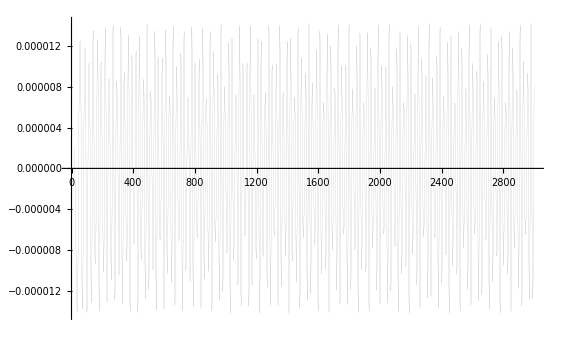

```mathematica
ListLinePlot[alldatahere[[2;;]],InterpolationOrder-> 2,PlotStyle->Directive[Opacity[0.5],AbsoluteThickness[0]],PlotTheme->"Monochrome",PlotMarkers->None]
```

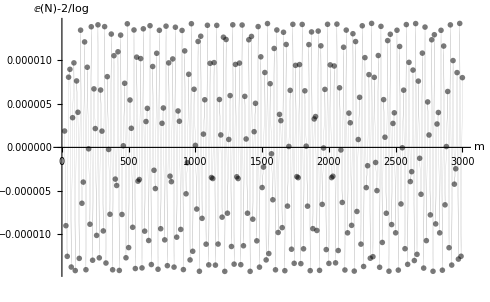

```mathematica
Show[%80,AxesLabel->{HoldForm[m],HoldForm[E[N]-2/log]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

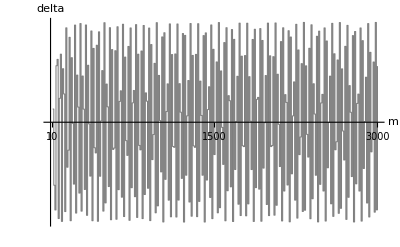

```mathematica
deltaplot=ListLinePlot[alldatahere[[2;;]],
Ticks->{{10,1500,3000},{.000015,-.000015}},
InterpolationOrder->0,
PlotStyle->Directive[Opacity[.5],AbsoluteThickness[.75]],
PlotTheme->"Monochrome",
PlotMarkers->None,
AxesLabel->{m,delta},
PlotLabel->None]
```

```mathematica
Export["deltaplot",deltaplot,"SVG"]
```

deltaplot

```mathematica
ExpandFileName["deltaplot"]
```

C:\Users\Spinoza\Documents\deltaplot

```mathematica
PMFS[n_,S_]:=2^(-S*Sum[l*2^-l,{l,1,n-1}])*(1-2^(-S*n*2^n))
```

```mathematica
Sum[PMFS[n,S],{n,1,S-1}]
```

```mathematica
FF[S_]:=∑_(n=1)^(-1+S) 2^(-2^(1-n) (-1+2^n-n) S) (1-2^(-2^n n S))
```

```mathematica
FF[10]//N
```

1.03232

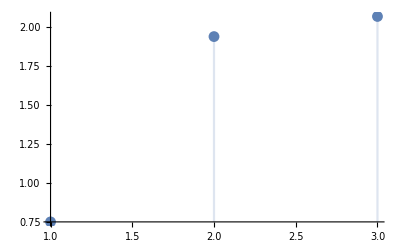

```mathematica
DiscretePlot[ExpectedLowerbound[S],{S,{1,2,3}}]
```

```mathematica
ExpectedLowerbound[5]//N
```

1.49832